```mathematica
(* GOAL: We'd like to find the integral of f[x] from 1/e to 1. See f: *)
f[x_] := -Log[-Log[-Log[x]]]
```

```mathematica
(* Before we get ahead of ourselves, let's see if we can find an exact integral / get better accuracy on Nint: *)
(* symbolic failed... *)
(* ZERO matches on the Inverse Symbolic Calculator. It's between -Psi(1/4)+Psi(2/5)+Psi(6/7)-Psi(11/12) and Prod(1+1/(2^n*(19/6*n^3-18*n^2+245/6*n-25)),n=1..inf) *)
NIntegrate[f[x],{x,1/E,1}]
```

0.1549

```mathematica
NumberForm[0.15489950476413913,16]
```

0.1548995047641391

```mathematica
(* Okay, so that didn't work. Big surprise there. Now, let's switch to a more general integral function and see if we can say anything about it! *)
(* plot of our integrand for a few different values of a *)
g[x_,a_]:=-Log[-Log[-Log[x]]]/(x^a)
Plot[{g[x,0],g[x,1],g[x,2],g[x,10],g[x,-1],g[x,-2],g[x,-10]},{x,0,1}]
```

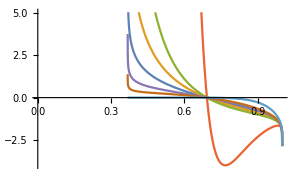

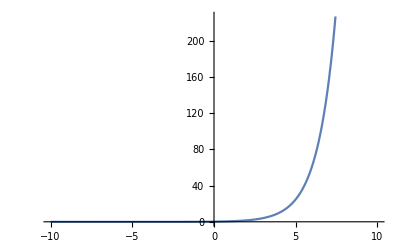

```mathematica
(* define our function I[a] (use different ident), plot it. It appears to be continuously differentiable for all Real a!!! *)
Aye[a_]:=NIntegrate[g[x,a],{x,1/E,1}]
Plot[Aye[a],{a,-10,10}]
(* It appears to blow up exponentially!*)
```

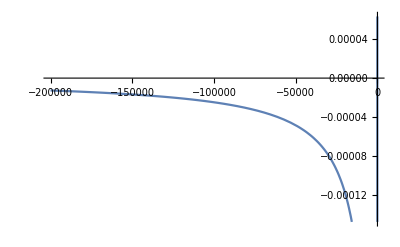

```mathematica
Plot[Aye[a],{a,-200000,1}]
```

```mathematica
(* OOH, that's cool. A bit of a perturbation near the origin. Let's compute the limit as a --> -inf.
```

```mathematica
vals = Array[-10*#&,100]
limtable = Map[Aye,vals]
```

{-10,-20,-30,-40,-50,-60,-70,-80,-90,-100,-110,-120,-130,-140,-150,-160,-170,-180,-190,-200,-210,-220,-230,-240,-250,-260,-270,-280,-290,-300,-310,-320,-330,-340,-350,-360,-370,-380,-390,-400,-410,-420,-430,-440,-450,-460,-470,-480,-490,-500,-510,-520,-530,-540,-550,-560,-570,-580,-590,-600,-610,-620,-630,-640,-650,-660,-670,-680,-690,-700,-710,-720,-730,-740,-750,-760,-770,-780,-790,-800,-810,-820,-830,-840,-850,-860,-870,-880,-890,-900,-910,-920,-930,-940,-950,-960,-970,-980,-990,-1000}

{-0.0908493,-0.0584791,-0.0432762,-0.0345148,-0.0287982,-0.0247622,-0.0217537,-0.0194208,-0.0175563,-0.0160305,-0.0147576,-0.0136788,-0.0127524,-0.0119478,-0.0112422,-0.0106181,-0.010062,-0.0095632,-0.0091132,-0.00870508,-0.00833317,-0.0079928,-0.00768007,-0.00739171,-0.00712493,-0.00687738,-0.00664701,-0.00643209,-0.00623108,-0.00604266,-0.00586567,-0.00569909,-0.00554202,-0.00539365,-0.00525327,-0.00512025,-0.00499401,-0.00487404,-0.00475988,-0.00465112,-0.00454737,-0.0044483,-0.00435358,-0.00426294,-0.00417612,-0.00409287,-0.00401297,-0.00393624,-0.00386247,-0.0037915,-0.00372317,-0.00365734,-0.00359386,-0.00353262,-0.00347349,-0.00341637,-0.00336115,-0.00330774,-0.00325606,-0.00320601,-0.00315753,-0.00311053,-0.00306495,-0.00302073,-0.00297781,-0.00293612,-0.00289562,-0.00285625,-0.00281797,-0.00278074,-0.0027445,-0.00270922,-0.00267487,-0.0026414,-0.00260878,-0.00257698,-0.00254597,-0.00251572,-0.0024862,-0.00245738,-0.00242925,-0.00240177,-0.00237492,-0.00234868,-0.00232303,-0.00229796,-0.00227343,-0.00224943,-0.00222596,-0.00220298,-0.00218048,-0.00215845,-0.00213688,-0.00211574,-0.00209503,-0.00207473,-0.00205483,-0.00203533,-0.00201619,-0.00199743}

```mathematica
(* Well this isn't too enlightening. All we know is it SEEMS to be monotonic and bounded, so in that case it WOULD converge. However we don't actually know if it's monotonic. We'd have to prove it somehow!!! *)
```

```mathematica
(* Next, let's try doing some sort of curve fit to our integral function I... *)
(* generate list of data *)
Table[Prime[x],{x,20}]
data = Table[Aye[a],{a,-100,25}]
FindFit[data,a*b^(x+c),{a,b,c},x]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

{-0.0160305,-0.0161705,-0.0163131,-0.0164584,-0.0166064,-0.0167572,-0.0169109,-0.0170676,-0.0172273,-0.0173902,-0.0175563,-0.0177258,-0.0178987,-0.0180753,-0.0182554,-0.0184394,-0.0186273,-0.0188193,-0.0190154,-0.0192159,-0.0194208,-0.0196303,-0.0198447,-0.020064,-0.0202884,-0.0205181,-0.0207534,-0.0209944,-0.0212412,-0.0214943,-0.0217537,-0.0220198,-0.0222928,-0.022573,-0.0228607,-0.0231561,-0.0234597,-0.0237717,-0.0240925,-0.0244225,-0.0247622,-0.0251119,-0.0254721,-0.0258433,-0.026226,-0.0266209,-0.0270283,-0.0274491,-0.0278839,-0.0283333,-0.0287982,-0.0292794,-0.0297778,-0.0302943,-0.03083,-0.0313859,-0.0319633,-0.0325635,-0.0331877,-0.0338376,-0.0345148,-0.0352211,-0.0359584,-0.0367288,-0.0375347,-0.0383785,-0.0392632,-0.0401917,-0.0411675,-0.0421943,-0.0432762,-0.0444179,-0.0456245,-0.0469017,-0.0482561,-0.0496948,-0.0512259,-0.0528587,-0.0546037,-0.0564726,-0.0584791,-0.0606385,-0.0629687,-0.06549,-0.0682255,-0.071202,-0.0744495,-0.0780017,-0.0818951,-0.0861669,-0.0908493,-0.0959578,-0.101464,-0.107237,-0.112913,-0.117608,-0.119257,-0.113108,-0.0881906,-0.018944,0.1549,0.577216,1.5956,4.05907,10.0617,24.8129,61.37,152.675,382.316,963.438,2441.96,6221.52,15923.4,40918.9,105525.,272998.,708244.,1.84204×10^6,4.80171×10^6,1.25424×10^7,3.28225×10^7,8.60391×10^7,2.25887×10^8,5.93888×10^8,1.56345×10^9,4.12088×10^9}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.17524×10^-8,b→1.65155,c→-45.9719}

```mathematica
(* DAMMIT. This is failing. We'll come bak to this l8r/ *)
```